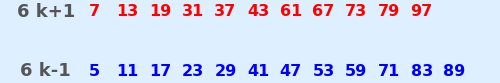

```mathematica
With[{t=Sequence[FontSize->16,FontFamily->"Cascadia Code",Bold],
s=Style[TraditionalForm[#],FontSize->18,FontFamily->"Times",Bold,Darker@Gray]&,
p=Select[Prime@Range@PrimePi@100,#~Mod~6==1&],
q=Select[Prime@Range@PrimePi@100,#~Mod~6==5&]},
Graphics[
Array[Text[Style[p[[#]],t,Red],{#,0}]&,Length@p]~Join~
Array[Text[Style[q[[#]],t,Blue],{#,-1}]&,Length@q]~Join~{
Text[s[6k+1],{-.5,0}],Text[s[6k-1],{-.5,-1}]
},ImageSize->500,AspectRatio->1/6,ImageMargins->15,Background->LightBlue]]
```

```mathematica
With[{p=Accumulate@Rest[Mod[Prime@Range[1500],6]/.{5->-1}]},
Manipulate[Show@{ListLinePlot[{Table[3,Min[100,s+5]],p⟦Max[s-100,1];;s⟧},Axes->False],
Graphics[Text[Style[Prime[s+1],Bold,FontSize->16],Center],ImageMargins->20]},
{{s,10},1,1490,1},LabelStyle->Tiny]]
```

```mathematica
FactorInteger[13,GaussianIntegers->True]
```

{{-ⅈ,1},{2+3 ⅈ,1},{3+2 ⅈ,1}}

```mathematica
Ramp[Prime@Range@PrimePi@1000~Mod~4-2]~FromDigits~2~IntegerString~"Base64"
```

Waa2M1anlUspsKx/KqptGbhLTPi2